# BesselK_0 distribution

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
http://www.eugenedeon.com/hitchhikers

```mathematica
BesselK0`pc[s_]:=2/Pi BesselK[0,s]
```

### Normalization

```mathematica
Integrate[BesselK0`pc[s],{s,0,Infinity}]
```

1

### Mean

```mathematica
Integrate[BesselK0`pc[s]s,{s,0,Infinity}]
```

2/π

### Moments

```mathematica
Integrate[BesselK0`pc[s] s^2,{s,0,Infinity}]
```

1

```mathematica
Integrate[BesselK0`pc[s] s^3,{s,0,Infinity}]
```

8/π

```mathematica
Integrate[BesselK0`pc[s] s^4,{s,0,Infinity}]
```

9

```mathematica
Integrate[BesselK0`pc[s] s^m,{s,0,Infinity},Assumptions->m>0]
```

(2^m Gamma[(1+m)/2]^2)/π

## GRT statistics

```mathematica
BesselK0`Xc[s_]:=1-s BesselK[0,s] StruveL[-1,s]-s BesselK[1,s] StruveL[0,s]
```

```mathematica
BesselK0`pu[s_]:=BesselK0`Xc[s] Pi/2
```

## Laplace representation

```mathematica
LaplaceTransform[2/(π  √(-1+q^2))HeavisideTheta[q-1],q,s]
```

(2 BesselK[0,s])/π

## Importance sampling / Random variate generation

Sample as a superposition of exponentials using the Laplace representation:

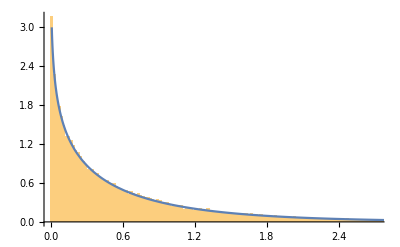

```mathematica
Show[
Histogram[Table[(Sec[(π RandomReal[])/2])^-1(-Log[RandomReal[]]),{i,Range[50000]}],450,"PDF"],
Plot[BesselK0`pc[s],{s,0,10},PlotRange->{0,3}]
]
```

## Laplace Transform

```mathematica
LaplaceTransform[BesselK0`pc[s],s,q]
```

(2 ArcCosh[q])/(π √(-1+q^2))

## Singular Eigenfunctions

```mathematica
c/2 Integrate[Exp[t u/v]BesselK0`pc[t],{t,0,Infinity},Assumptions->v>0&&-1<u<1]
```

ConditionalExpression[(c v (π-ArcCos[u/v]))/(π √(-u^2+v^2)),u≤0]

## Fourier Propagator

The dD Fourier propagator for the BesselK0 distribution is

```mathematica
πd[d,BesselK0`pc[r]]
```

Hypergeometric2F1[1/2,1/2,d/2,-z^2]

## Grosjean F functions

```mathematica
pc=c BesselK0`pc[#]&
```

c BesselK0`pc[#1]&

```mathematica
Fpc[0,0,pc,z]
```

(c ArcSinh[z])/z

```mathematica
Fpc[1,0,pc,z]
```

-(2 c (z-√(1+z^2) ArcSinh[z]))/(π z^2)

```mathematica
Fpc[1,1,pc,z]
```

(c (z √(1+z^2)-ArcSinh[z]))/(2 z^3)

```mathematica
Fpc[2,0,pc,z]
```

(c (-3 z √(1+z^2)+(3+2 z^2) ArcSinh[z]))/(4 z^3)

```mathematica
Fpc[2,1,pc,z]
```

(2 c (3 z+z^3-3 √(1+z^2) ArcSinh[z]))/(3 π z^4)

```mathematica
Fpc[2,2,pc,z]
```

(c (-3 z √(1+z^2) (9+2 z^2)+(27+24 z^2+8 z^4) ArcSinh[z]))/(32 z^5)

```mathematica
Fpc[k,0,pc,z]
```

(c z^k Gamma[(1+k)/2]^2 Hypergeometric2F1Regularized[(1+k)/2,(1+k)/2,3/2+k,-z^2])/(2 √π)

```mathematica
Fpc[k,1,pc,z]
```

ConditionalExpression[-1/(16 √π)c z^(-1+k) Gamma[k/2]^2 (-4 Hypergeometric2F1Regularized[k/2,k/2,1/2+k,-z^2]+2 Hypergeometric2F1Regularized[k/2,k/2,3/2+k,-z^2]+k^2 z^2 Hypergeometric2F1Regularized[(2+k)/2,(2+k)/2,5/2+k,-z^2]),k>0]